0.5 Erf[10.6066-3.53553 A]+0.5 Erf[3.53553+3.53553 A]

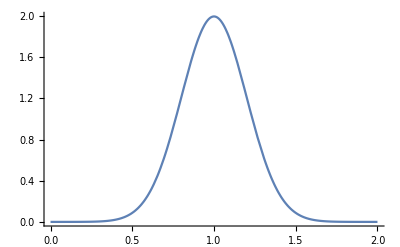

-Graphics3D-

-Graphics3D-

```mathematica
s=0.2;
m=1;
psir=N[Exp[-(r-m)^2/(2 s^2)]/(s √(2 π))];
dpsir=N@D[Exp[-(r-m)^2/(2 s^2)]/(s √(2 π)),r];
psi=psir/.r->√(x^2+y^2);
psic=Compile[{{x,_Real},{y,_Real}},Exp[-(√(x^2+y^2)-m)^2/(2 s^2)]/(s √(2 π))];
signifPts[a_,n_,eps_]:=Select[Flatten[Table[{x,y},{x,-n,n},{y,-n,n}],1],a^-1 psic[N[a^-1#⟦1⟧],N[a^-1#⟦2⟧]]>eps&];
dpsi[x_,y_]:=dpsir/.r->√(x^2+y^2);
a=1.0;
ia=a^-1;
pr=2a;
Integrate[a^-1*psir/.{r->a^-1*t},{t,A-pr,A+pr}]
Plot[a^-1*psir/.{r->a^-1*t},{t,0,pr},PlotRange->All]
Plot3D[IA*psic[a^-1*x,a^-1*y],{x,-pr,pr},{y,-pr,pr},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->50]
Plot3D[a^-1*dpsi[a^-1*x,a^-1*y],{x,-pr,pr},{y,-pr,pr},PlotRange->All,ColorFunction->"TemperatureMap",PlotPoints->50]
```

```mathematica
a=1;
NIntegrate[a^-1(√(x^2+y^2))^-1 Exp[-(a^-1 √(x^2+y^2)-m)^2/(2 s^2)]/(s √(2 π)),{x,a(-m-3s),a(m+3s)},{y,a(-m-3s),a(m+3s)}]
NIntegrate[a^-2 Exp[-(a^-1 √(x^2+y^2)-m)^2/(2 s^2)]/(s √(2 π)),{x,a(-m-3s),a(m+3s)},{y,a(-m-3s),a(m+3s)}]
N[2π]
```

6.28067

6.27896

6.28319

```mathematica
img=Image[Graphics[{EdgeForm[{Thickness[0.03],White}],White,Rectangle[{2,1}],{Thickness[0.03],Black,Circle[{2,2},0.5]}},ImageSize->200]]
f=Map[1.0-Total[#]/N[255*3]&,ImageData[img,"Byte"],{2}];
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["f.tsv",f, "Table"]
```

f.tsv

```mathematica
(*SetDirectory[NotebookDirectory[]];
wf=Import["wf.ssv","Table"];
min=Min@Flatten@wf;
diff=Max@Flatten@wf-minwf;
nwf=Map[1.0-(#-min)/diff&,wf,{2}];
Image[nwf]*)
```

```mathematica
wfs=SequenceSplit[Import["wfs.ssv","Table"],{{}}];
wwfs=SequenceSplit[Import["wwfs.ssv","Table"],{{}}];
nwfs=Map[
With[{min=Min@Flatten@#,diff=Max@Flatten@#-Min@Flatten@#},Map[1.0-(#-min)/diff&,#,{2}]]&,
wfs];
nwwfs=Map[
With[{min=Min@Flatten@#,diff=Max@Flatten@#-Min@Flatten@#},Map[1.0-(#-min)/diff&,#,{2}]]&,
wwfs];
wimgs=Map[Image@#&,nwfs];
wwimgs=Map[Image@#&,nwwfs];
Manipulate[{wimgs⟦i⟧,wwimgs⟦i⟧},{i,1,Length@wimgs,1}]
```

```mathematica
cnwwfss=Table[Map[If[#>t,1.0,#]&,nwwfs,{3}],{t,0.0,1.0,0.1}];
cwwimgss=Map[Image@#&,cnwwfss,{2}];
Manipulate[cwwimgss⟦t,i⟧,{t,1,10,1},{i,1,Length@wimgs,1}]
```

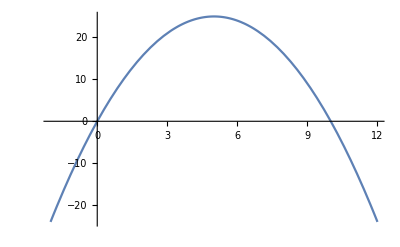

```mathematica
m=5;
s=5;
Plot[s^2-(r-m)^2,{r,m-s-2,m+s+2}]
```